Université Pierre et Marie Curie |                                                                          | UE 4M062 Mathematica

__________________________________________________________________________

M 2 : Utilisation de Mathematica
__________________________________________________________________________

## Préambule

## I. Calculs formels

### A. Fonctions essentielles

Mathematica est capable d’effectuer toutes sortes de calculs formels que nous allons illustrer simplement :

#### 1. ==

La première fonction est == qui indique si les expressions placées à droite et à gauche sont identiques. C’est le cas pour les expressions ci-dessous : comme on peut le vérifier, l’évaluation renvoie “True”.

Dans la suite, par souci de compacité et de clarté d’écriture de ce texte, nous condenserons sur la même ligne la requête initiale à gauche du signe == et le résultat à droite (True étant implicite).

```mathematica
Pi==π
Factorial[n]==n!
Sin[x]^2+Cos[x]^2==Sin[x]^2+Cos[x]^2
```

Dans ces trois exemples, c’est un simple test d’égalité de différentes écritures d’une même expression.

Dans les exemples ci-dessous, Mathematica ne fait pas seulement un simple test d’égalité. En effet, associé à l’évaluateur de Mathematica (boucle infinie qui réécrit l’expression jusqu’à ce qu’elle soit simple, cf. M1), ces tests d’égalité (qui renvoient “True”) sont des prétextes ou des exemples de réécritures sur les nombres entiers :

```mathematica
1/(1/3+1/2)==6/5
```

```mathematica
5/7-2/7(1-3/4)==18/28
```

On imagine assez facilement comment fonctionne l’évaluateur de Mathematica il effectue systématiquement une suite de factorisations en facteurs premiers, de réarrangements et de simplifications, sans doute du type ci-dessous, de chacun des deux membres qu’il ramène à une expression unique (9/14) :

```mathematica
5/7-2/7(1-3/4)==1/7(5-2(1/4))==1/7(5-1/2)==1/7(10/2-1/2)==1/7(9/2)==18/28
```

On observe et on peut vérifier que toutes ces opérations sont faites automatiquement (sans qu’il soit nécessaire de faire appel à une fonction particulière de ) et qu’elles renvoient toutes “True”.

Application : Ces deux nombres sont très particuliers : en quoi ?
	(-7-4 √2-2 √(2 (10+7 √2)))       (-7-4 √2+2 √(2 (10+7 √2)))

Montrer que le produit de ces 2 deux nombres vaut 1 :
	C’est facile à faire numériquement, mais vous n’avez pas prouvé que ce produit vaut exactement 1.

```mathematica
N[(-7-4 √2-2 √(2 (10+7 √2)))(-7-4 √2+2 √(2 (10+7 √2)))]
```

1.

Montrer que ce produit vaut exactement 1 au moyen d’une suite d’expressions.
Au total ces deux nombres sont exactement inverses l’un de l’autre, et s’écrivent avec les mêmes nombres.
La simplification que vous avez réalisée vous-même vous permet de comprendre (un peu) mieux comment ces deux nombres ont été construits. Ce que ne donne pas Mathematica a priori.

```mathematica
(* En remarquant que c'est un produit du type (a-b)(a+b), et en développant, on vérifie qu'il vient successivement : *)(-7-4 √2-2 √(2 (10+7 √2)))*(-7-4 √2+2 √(2 (10+7 √2)))==((-7-4 √2)^2-(2 √(2 (10+7 √2)))^2)==
(49+32+56 √2-(4 2 (10+7 √2)))==
(81+56 √2-80-56 √2)==1//Simplify
```

Mais on observe que Mathematica n’effectue les simplifications qu’au niveau prescrit comme on peut le constater :

```mathematica
Sin[x]^2+Cos[x]^2==1
```

Cos[x]^2+Sin[x]^2==1

Mathematica renvoie la meilleure expression possible selon les prescriptions données. Pour que Mathematica reconnaisse cette expression comme vraie, il faut lui prescrire l’utilisation des règles trigonométriques.

#### 2. Autres tests

Test : | non-égalité | supériorité | supériorité ou égalité | infériorité ou égalité
Code : | x!=y | x>y | x>=y | x<y
Apparence : | x≠y | x>y | x≥y | x<y

Pour combiner des expressions logiques avec un :
	“ET” logique ("&&" en Mathematica), ou
	"OU" logique ("| |" en Mathematica).

Par exemple :	pour tester si  x<0  ET y=0, on écrit :	x<0&&y==0
		pour tester si  x<0  OU y=0, on écrit :	x<0||y==0

#### 3. Simplify

La fonction Simplify[] recherche à réécrire l’argument sous la forme la plus simple possible, en utilisant les transformations algébriques et trigonométriques habituelles.

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

Dans le cas où l’argument comporte implicitement deux membres comme dans l’exemple ci-dessous : la fonction Simplify[] recherche à réécrire chacun des membres sous la forme la plus simple possible de la même manière :

```mathematica
Simplify[Sin[x]^2+Cos[x]^2==1]
```

Une simplification n’est pas toujours (ou plutôt beaucoup plus qu’attendu!) mathématiquement possible :

```mathematica
Simplify[Abs[Cos[x]]==Cos[x]]
```

Abs[Cos[x]]==Cos[x]

Aussi faut-il rajouter les bonnes conditions : ce que nous allons voir au point suivant avec Assumptions.

La fonction FullSimplify[] procède comme Simplify[] utilisant une base de transformations encore plus large, et notamment en utilisant les (ou des) fonctions spéciales. L’inconvénient est qu’elle peut prendre beaucoup (trop) de temps, et donc on ne l’utilise éventuellement que si Simplify[] ne suffit pas.

#### 4. Simplify avec Assumptions

```mathematica
Simplify[Abs[Cos[x]]==Cos[x], x>0]
Simplify[Abs[Cos[x]]==Cos[x], x<0]
Simplify[Abs[Cos[x]]==Cos[x], 0<x<π]
```

Abs[Cos[x]]==Cos[x]

Abs[Cos[x]]==Cos[x]

Abs[Cos[x]]==Cos[x]

Si Mathematica ne peut donner sens à ce que vous proposez, il ne peut que recopier l’expression de départ ...
Il faut connaître un peu de Mathématiques, et notamment la définition de la valeur absolue...

On peut aussi donner plusieurs suppositions avec les connecteurs logiques (&& veut dire ET, || veut dire OU) :

```mathematica
Simplify[Abs[Cos[x]]==Cos[x], 0<x<π/2]
Simplify[Abs[Cos[x]]==Cos[x], -π/2<x<π/2]
Simplify[Abs[Cos[x]]==Cos[x], -π/2<x<π/2 && (-π/2+2π<x<π/2+2π)]
```

True

True

Simplify::cas: Warning: Contradictory assumption(s) -π/2 < x < π/2 && 3\ π/2 < x < 5\ π/2 encountered.

True

Ce n’est pas parce qu’on a trouvé une solution, qu’on a trouvé toutes les solutions.
En réalité ici, la “bonne” solution est donnée par la définition de la valeur absolue :
Simplify[Abs[Cos[x]] == Cos[x], Cos[x] > 0]
True

Retenir :

```mathematica
Simplify[Sqrt[x^2]]                    (* Pas de simplification possible *)
```

```mathematica
Simplify[Sqrt[x^2],x≥0]==x    (* True *)
```

PowerExpand[] suppose toujours que x≥0 et donc :

```mathematica
PowerExpand[Sqrt[x^2]]==x           (* True *)
```

C’est donc une fonction très pratique quand on est sûr que x est positif.

#### 5. Simplify avec Assumptions et Element

On peut aussi spécifier le domaine d’une variable avec la fonction Element[]. Imposons que x soit réel :

```mathematica
Simplify[Sqrt[x^2],Element[x,Reals]]==Simplify[√(x^2),x∈Reals]==Abs[x]         (* True *)
```

Par défaut, Mathematica suppose que toutes les variables symboliques sont complexes (c’est le cas le plus général), et donc Mathematica ne peut opérer une réelle simplification que si on lui spécifie que x est réel.

Définir une variable n^(.08) entier peut être utile pour les fonctions trigonométriques :

```mathematica
Element[(n-1)/4,Integers]
```

1/4 (-1+n)∈Integers

Que donnent ?

```mathematica
Simplify[Sin[x+2*n*Pi],Element[n,Integers]]
Simplify[Cos[n*Pi/2-x],Element[(n-1)/4,Integers]]
```

Sin[x]

Sin[x]

Ce sont des identités trigonométriques : expliquez pourquoi sur le cercle trigonométrique.

On peut aussi combiner Element[] avec d’autres conditions (Laquelle permet de simplifier ?) :

```mathematica
Simplify[Log[x^r]]
Simplify[Log[x^r],x>0]
Simplify[Log[x^r],Element[r,Reals]]
Simplify[Log[x^r],x>0&&Element[r,Reals]]
```

Log[x^r]

Log[x^r]

Log[x^r]

r Log[x]

Par défaut, les variables symboliques sont complexes (c’est le cas le plus général), et donc Mathematica ne peut opérer une réelle simplification que si on lui spécifie que x>0 et r est réel.

#### 6. Application

Comment se simplifie l’expression suivante : 5 ln a^2− 2 ln a ?

```mathematica
Simplify[5 Log[ a^2]− 2 Log[ a]==5 Log [a^2]-Log [a^2]==4 Log [a^2]==Log[ a^8],a> 0]
```

Autrement dit, cette simplification n’est vraie que si a est un réel positif.

#### 7. Pour aller plus loin : les domaines ℂ, ℝ, 𝔸, ℚ, ℕ, Premiers

Cf. aide de Mathematica guide/AssumptionsAndDomains ou tutorial/UsingAssumptions pour trouver la liste des Domains.

Complexes | the domain of complex numbers ℂ
Reals | the domain of real numbers ℝ
Algebraics | the domain of algebraic numbers 𝔸
Rationals | the domain of rational numbers ℚ
Integers | the domain of integers ℤ
Primes | the domain of primes ℙ

En regardant le sous-point Properties&Relations de l’aide sur Algebraics, définir quels domaines Algebraics contient et ne contient pas, ainsi que dans quels domaines Algebraics est contenu ou pas.
(cf.	http://fr.wikipedia.org/wiki/Nombre_algébrique )

Algebraic numbers are defined to be numbers that solve polynomial equations with rational coefficients.

Algebraics contient Rationals, Integers et Primes, mais pas Reals ou Complexes

```mathematica
Refine[
Element[x,Algebraics],Element[x,#]
]&/@{Rationals,Integers,Primes}
```

{True,True,True}

Algebraics est contenu dans les Complexes

```mathematica
Refine[
Element[x,Complexes],Element[x,Algebraics]
]==True
```

Algebraics est contenu dans Complexes, mais pas dans Reals

```mathematica
Element[Pi, Reals]                                            (* True *)
Element[Pi, Algebraics]                                 (* False *);
```

```mathematica
Element[(6+I Sqrt[5])^(1/3),Algebraics] (* True *)
Element[(6+I Sqrt[5])^(1/3),Complexes]    (* True *)
Element[(6+I Sqrt[5])^(1/3),Rationals]    (* False *);
```

```mathematica
Element[(6+I*Pi)^(1/3),Complexes]              (* True *)
Element[(6+I*Pi)^(1/3),Algebraics]            (* False *);
```

### B. Fonction pure

#### 1. Définition

Les fonctions anonymes, encore appelées fonctions pures dans Mathematica, sont des fonctions qui n’ont pas de nom.

En pratique c’est le code même de la fonction qui est utilisé comme nom ou comme moyen ou d’utiliser la fonction. Exemple : pour coder : f[x_]:=x^3+4, on écrit :

```mathematica
(#^3+4)&
```

Pour calculer la fonction en x=5, f[5]^(.08), il suffit d’écrire le code suivi de l’argument entre crochets :

```mathematica
(#^3+4)&[5]
```

129

Le rôle de la variable muette est tenu par #, et la fin de la fonction pure est marquée par &. Toutefois, pour une lecture plus claire, c’est une bonne pratique de bien repérer le début et la fin de la fonction par des ( ), toujours suivies de &.

Les fonctions pures sont une notion importante de la programmation fonctionnelle. Par construction, pour être utilisées, le nom des fonctions doit être répertorié dans un tableau propre au système qui est consulté chaque fois que l’on recherche la définition d’une fonction portant un nom donné. Pour éviter cette recherche de nom coûteuse en temps de calcul, on peut définir des fonctions pures localement au moment de leur utilisation.

#### 2. Intérêts pratiques

C’est essentiellement un moyen pratique pour Mathematica de communiquer une fonction, comme l’expression de la solution d’un système d’équations différentielles. C’est aussi un moyen de contrôler certaines fonctions très utilisées comme Select[]. Pour ces raisons, il est indispensable de connaître le mode de définition et d’utilisation des fonctions pures.

Toutefois, c’est un mode d’écriture qui est généralement à proscrire car très peu lisible et difficile à documenter.

#### 3. Application

Les nombres premiers ne peuvent pas être multiples de 2, ni de 4, ils sont au plus de la forme : 4 n + 1 ou 4 n -1. 
Construisons et testons une fonction pure qui ne retient que les nombres multiples de 4 augmentés de 1 (elle ne renvoie que True ou False).

Une façon de faire (cf. Aide pour IntegerQ[]) :

```mathematica
(IntegerQ[(#-1)/4])&[8]
```

False

```mathematica
(IntegerQ[(#-1)/4])&[9]
```

True

Une autre façon de faire (cf. Aide pour Mod[]) :

```mathematica
(Mod[#-1,4]==0)&[7]
```

False

```mathematica
(Mod[#-1,4]==0)&[9]
```

True

Tests :

```mathematica
((Mod[#-1,4]==0 )||(Mod[#+1,4]==0))&[7]
((Mod[#-1,4]==0 )||(Mod[#+1,4]==0))&[8]
((Mod[#-1,4]==0 )||(Mod[#+1,4]==0))&[9]
```

True

False

True

On peut ainsi s’en servir pour construire une liste :

```mathematica
Select[Range[20],(IntegerQ[(#-1)/4])&]
```

{1,5,9,13,17}

## II. Listes

### A. Définition et Opérations immédiates

#### 1. Définition

Par définition une liste dans Mathematica est une suite d’expressions : c’est donc une famille ordonnée d’expressions.

Plus concrètement une liste est un ensemble ordonné (avec répétition ou non) de n’importe quelles expressions (nombres, variables, symboles, fonctions, graphiques, ou même des listes, des listes de listes, ...) séparées par des virgules et regroupées entre accolades.

```mathematica
liste1={a, b, c}
```

liste1 est une liste, où a, b, c peuvent être des expressions quelconques :

```mathematica
liste2={{a,3},b,{titi,f[x],-√57},grosminet}
```

#### 2. Adressage

D’un point de vue informatique, en première approximation, une liste est un tableau indexé implicitement. 
On peut donc adresser simplement ses éléments. Étant donné que :
	les simples crochets sont déjà réservés pour définir les fonctions fonction[]
	les accolades sont utilisées pour les listes
	et que les () servent au regroupement d’expressions comme dans : (2+3) ×5
l’adressage est obtenu dans Mathematica au moyen de double crochets, ainsi :

```mathematica
liste1[[1]]
```

a

```mathematica
liste1[[3]]
```

c

```mathematica
liste2[[3]]
```

{titi,f[x],-√57}

En seconde approximation, les éléments du “tableau” n’étant pas de même nature, une liste peut donc être un tableau de structures génériques, ou une structure.

Pour éviter l’effet visuel perturbant des doubles crochets, on utilise souvent un équivalent plus esthétique avec des raccourcis clavier Esc[[Esc et Esc]]Esc  pour rendre les doubles crochets plus compacts :

```mathematica
liste2⟦4⟧
```

grosminet

#### 3. La propriété “Listable” de fonctions Mathematica

De nombreuses fonctions Mathematica et notamment les opérations ordinaires ont la propriété d’être “Listable” : cela signifie que cette fonction f peut être appliquée directement à une liste {a,b,c} pour donner la liste des images de cette fonction par f : {f[a],f[b],f[c]} :

```mathematica
liste3={3,5,11,13,25,36,77}
```

On peut donc faire directement des opérations sur les listes.

Les quatre opérations (renvoient toutes “True”) :

```mathematica
2+liste3=={5,7,13,15,27,38,79}
liste3-39=={-36,-34,-28,-26,-14,-3,38}
2*liste3=={6,10,22,26,50,72,154}
liste3/3=={1,5/3,11/3,13/3,25/3,12,77/3}
```

Fonctions élémentaires (renvoient toutes “True”) :

```mathematica
liste3^2=={9,25,121,169,625,1296,5929}
liste3*liste3=={9,25,121,169,625,1296,5929}
Sqrt[liste3]=={√3,√5,√11,√13,5,6,√77}
Log[liste3]=={Log[3],Log[5],Log[11],Log[13],Log[25],Log[36],Log[77]}
```

liste3 est un vecteur qui comporte 7 entrées.

La propriété “Listable” est une propriété d’opérations élémentaires très pratique sur les vecteurs. Elle est effectuée directement sans boucle de programmation pour construire l’opération.

#### 4. Opérations terme à terme, et fonctions “Listable”

Soit la liste :

```mathematica
liste4={1,2,3,4,5,6,7}
```

liste3 et liste4 sont des vecteurs de même “nature” comprenant chacun 7 entrées.
Toutes les opérations terme à terme sont alors possibles directement (renvoient toutes “True”) :

```mathematica
liste3+liste4=={4,7,14,17,30,42,84}
liste3-(2*liste4)=={1,1,5,5,15,24,63}
liste3*liste4=={3,10,33,52,125,216,539}
liste3/liste4=={3,5/2,11/3,13/4,5,6,11}
```

Si les listes ne sont pas de même nature, les opérations sont (évidemment) impossible comme le dit fort bien Mathematica.

Soient les listes :

```mathematica
liste5={1,2,3,4,5,6,7,8};
liste6={1,2,3,{4,4},5,6,7};
```

```mathematica
liste3+liste5
```

Thread::tdlen: Objects of unequal length in {3, 5, 11, 13, 25, 36, 77} + {1, 2, 3, 4, 5, 6, 7, 8} cannot be combined.

{3,5,11,13,25,36,77}+{1,2,3,4,5,6,7,8}

C’est écrit en rouge, certes ! Mais ce ne sont pas des insultes : Mathematica vous explique au mieux pourquoi il ne peut pas faire l’opération. Ce sont au contraire des indications très précieuses !

Attention toutefois à des effets moins attendus, mais tout aussi logiques :

```mathematica
liste3+(2*liste6)
```

{5,9,17,{21,21},35,48,91}

### B. Générations de listes

#### 1. Range[]

La fonction Range[] génère une liste très simple (unidimensionnelle) de nombres (pas de symboles) (cf. aide) avec les exemples respectifs :

```mathematica
?Range
```

Range[i_max] generates the list {1,2,…,i_max}. 
Range[i_min,i_max] generates the list {i_min,…,i_max}. 
Range[i_min,i_max,di] uses step di.

```mathematica
Range[10]
Range[3.1,8.5]
Range[3.1,8.5,0.5]
```

{1,2,3,4,5,6,7,8,9,10}

{3.1,4.1,5.1,6.1,7.1,8.1}

{3.1,3.6,4.1,4.6,5.1,5.6,6.1,6.6,7.1,7.6,8.1}

#### 2. Table[]

La fonction Table[] autorise beaucoup plus de souplesse :
L’élément générique de la liste est une expression (pas seulement numérique, mais pratiquement toute expression...). De plus les indices sont explicitement utilisés, ce qui autorise des listes multidimensionnelles et des contrôles pour générer la liste (cf. aide) avec les exemples respectifs :

```mathematica
?Table
```

RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]], "}"}]}], "]"}] generates a list of SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]] copies of StyleBox["expr", "TI"]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a list of the values of StyleBox["expr", "TI"] when StyleBox["i", "TI"] runs from 1 to SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] starts with RowBox[{StyleBox["i", "TI"], "=", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]]}]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]], ",", StyleBox["di", "TI"]}], "}"}]}], "]"}] uses steps StyleBox["di", "TI"]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "}"}]}], "]"}] uses the successive values SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ….
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["j", "TI"], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] gives a nested list. The list associated with StyleBox["i", "TI"] is outermost.

```mathematica
Table["Coucou",{5}]
Table[i,{i, 10}]
Table[{i,i^2},{i, 3.1,8.5}]
liste7=Table[{i,i^2},{i, 3.1,8.5,0.5}]
```

{Coucou,Coucou,Coucou,Coucou,Coucou}

{1,2,3,4,5,6,7,8,9,10}

{{3.1,9.61},{4.1,16.81},{5.1,26.01},{6.1,37.21},{7.1,50.41},{8.1,65.61}}

{{3.1,9.61},{3.6,12.96},{4.1,16.81},{4.6,21.16},{5.1,26.01},{5.6,31.36},{6.1,37.21},{6.6,43.56},{7.1,50.41},{7.6,57.76},{8.1,65.61}}

#### 3. Comparaison des vitesses de calcul de Range[] et de Table[]

La fonction Range[] opère très rapidement sur des nombres.
La fonction Table[] perd en rapidité ce qu’elle gagne en puissance et souplesse : cf. évaluation cachée.

→ Générez de 2 façons différentes la liste des multiples de 7 positifs de 1 à 100 :

```mathematica
Range[7,100,7]
```

{7,14,21,28,35,42,49,56,63,70,77,84,91,98}

```mathematica
Table[i, {i, 7,100,7}]
```

{7,14,21,28,35,42,49,56,63,70,77,84,91,98}

→ Quelle est la méthode la plus rapide ? (testez pour cette même liste de 1 à 10^9)

```mathematica
Range[7,10^9,7];//Timing
```

{0.393672,Null}

```mathematica
Table[i, {i, 7,10^9,7}];//Timing
```

{5.88461,Null}

#### 4. Génération fonctionnelle de listes (Voir ultérieurement)

Mentionnons seulement la génération fonctionnelle de listes avec NestList[], NestWhileList[], FoldList[], ...	cf. Aide

#### 5. Génération procédurale de listes (Supplément)

(Supplément : peut être sauté en première lecture ; utile pour M8)
Génération procédurale de listes avec Do[], For[], While[] ...	cf. Aide

Nous allons illustrer un élément important de programmation procédurale avec la boucle Do[].
For[], While[] ... sont assez similaires, et ne sont pas abordés ici (cf. Aide).

Une boucle "Do" permet d'exécuter plusieurs fois une instruction. (Le mot instruction est plutôt réservé à la programmation procédurale. Do[] de Mathematica est plus générale puisqu’elle peut traiter une expression.)

La commande :
	Do[instruction, {i, idebut, ifin}]
fait varier l'indice entier "i" (appelé "itérateur") de l'entier "idebut" à l'entier "ifin" et exécute à chaque fois "instruction". Par exemple, pour afficher "Coucou" 3 fois, on utilise une boucle Do exécutant l'instruction Print["Coucou"] lorsque i varie de 1 jusqu'à 3 :

```mathematica
Do[Print["   Coucou"],{i,1,3}]
```

Coucou

Coucou

Coucou

Les boucles Do sont plus intéressantes si on a besoin d'utiliser l'entier i dans l'instruction. Par exemple, affichons les 3 premiers entiers :

```mathematica
Do[Print["   ",i],{i,1,3}]
```

1

2

3

Utilisons une boucle Do pour calculer la somme des 100 premiers entiers s=∑_(i=1)^100 i. Trois étapes sont nécessaires :

1./ On commence par initialiser la variable s à 0 :

```mathematica
s=0;
```

2./ Puis on fait varier i de 1 jusqu'à 100 par pas de1, et à chaque itération on calcule s+i et on affecte le résultat obtenu à la variable s :

```mathematica
Do[s=s+i,{i,1,100}]
```

3./ À la fin des itérations, la variable s contient la somme recherchée :

```mathematica
s
```

5050

Il est souvent plus clair (et un peu plus sûr) de regrouper ces trois instructions dans une seule cellule en les séparant par des ";" (qui suppriment les affichages intermédiaires)

```mathematica
s=0;
Do[s=s+i,{i,1,100}];
s
```

On remarque que l’on a fait une opération sur une séquence de nombres sans avoir besoin de générer une liste. À chaque étape, on ne traite que deux nombres à la fois, et rien de plus. Dans un langage compilé (C, Fortran, ...), cette méthode de calcul “dans la mémoire” de l’ordinateur est très efficace. Dans Mathematica cette efficacité est souvent bonne, mais n’est pas forcément toujours garantie.

De même pour générer une liste, il faut :
1./ déclarer une liste vide, que l’on va remplir : listeResultatDo
2./ réécrire à chaque étape cette liste avec l’élément en plus : listeResultatDo=Append[listeResultatDo,i]
3./ on vérifie la construction de la liste en l’affichant à la fin

```mathematica
listeResultatDo ={};
Do[
listeResultatDo=Append[listeResultatDo,i],
{i,1,100}
];
listeResultatDo
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

Les boucles Do[] (comme Table[]) permettent de faire beaucoup de constructions, et notamment celles ci-dessous :

Par défaut, l'itérateur varie par incrément de 1, mais on peut aussi utiliser n'importe quel autre incrément. Par exemple, dans la boucle Do suivante l'entier j varie de 3 jusqu'à 10 par incrément de 2

```mathematica
Do[Print[j],{j,3,10,2}]
```

Et dans la boucle suivante l'entier j varie de 5 jusqu'à 2 par incrément de -1

```mathematica
Do[Print[j],{j,5,2,-1}]
```

Enfin, on peut exécuter plusieurs intructions dans une boucle Do en les séparant par ";". Par exemple, calculons la somme s et le produit p des 10 premiers entiers, s=∑_(i=1)^100 i et p=∏_(i=1)^10 i, avec une seule boucle Do :

```mathematica
s=0;p=1;
Do[
s=s+i;p=p*i,
{i,1,10}
];
Print[s];
Print[p];
```

55

3628800

### C. Opérations sur les listes

#### 1. Transposition d’une liste : Transpose[]

La fonction Transpose[tf] permet d’inverser la liste tf = { {x1, y1}, {x2, y2}, ...} qui devient après transposition { {x1, x2, ...}, {y1, y2, ...} } (cf. aide) :

```mathematica
?Transpose
```

Transpose[list] transposes the first two levels in list. 
Transpose[list,{n_1,n_2,…}] transposes list so that the k^th level in list is the n_k^th level in the result.

```mathematica
tf={{a,b,c},{x,y,z}}
Transpose[tf]
Transpose[Transpose[tf]]==tf
```

{{a,b,c},{x,y,z}}

{{a,x},{b,y},{c,z}}

True

#### 2. Traitement individuel de chaque élément d’une liste : Map[]

Une fonction quelconque f n’a pas a priori la propriété “Listable” :

```mathematica
f[liste3]
```

f[{3,5,11,13,25,33,78}]

Mais il est possible de faire l’opération équivalente avec la fonction Map[] :

```mathematica
Map[f,liste3]
```

{f[3],f[5],f[11],f[13],f[25],f[33],f[78]}

#### 3. Traitement global d’une liste : Apply[]

La fonction Apply[fonction, liste]  (cf. aide) est une belle illustration de programmation fonctionnelle par ré-écriture d’expressions pour obtenir une nouvelle fonction. En effet la représentation fonctionnelle de liste1 est :

```mathematica
liste1=={a,b,c}==List[a,b,c]                                          (* True *)
```

La fonction Plus[] a le même format de représentation fonctionnelle :

```mathematica
a+b+c==Plus[a,b,c]                                                                 (* True *)
```

Les noms des fonctions List et Plus sont appelées “Head” ou tête de la fonction représentée en notation fonctionnelle standard.

```mathematica
Head[a+b+c]
```

Plus

Pour faire la somme des éléments de liste, il suffit donc de changer la “tête” en transformant le nom de l’un (List) en celui de l’autre (Plus). C’est le rôle de Apply[].

```mathematica
Apply[Plus,liste1]==Plus[a,b,c]==a+b+c              (* True *)
```

#### 4. Sélection dans une liste : Select[]

La fonction Select[liste, critère] sélectionne dans une “liste” les éléments qui satisfont le “critère” (cf. aide).

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True.

Pour ne retenir que les nombres impairs :

```mathematica
Select[{1,2,3,4,5,6,7,8,9,10},OddQ]
```

{1,3,5,7,9}

Pour ne retenir que les nombres premiers :

```mathematica
Select[{1,2,3,4,5,6,7,8,9,10},PrimeQ]=={2,3,5,7}       (* True *)
```

Le critère est ici une fonction pure (#>3)&) pour ne retenir que les éléments plus grands que 3 :

```mathematica
Select[{1,2,3,4,5,6,7,8,9,10},( #>3)&]
```

{4,5,6,7,8,9,10}

Le critère est ici une fonction pure (#^2>3#+4)& pour ne retenir que les éléments dont le carré est plus grand que 3 fois le nombre plus 4 :

```mathematica
Select[{1,2,3,4,5,6,7,8,9,10},( #^2>3#+4)&]
```

{5,6,7,8,9,10}

Exemple résolu d’application :
Utiliser la fonction pure établie plus haut pour ne retenir que les nombres de la forme : 4 n + 1 ou 4 n -1.

```mathematica
liste0=RandomInteger[{1,1000},{100}]
```

{630,766,149,149,688,609,523,72,538,916,116,445,947,421,741,771,424,655,471,709,139,208,408,77,77,52,446,684,698,259,1,384,903,152,160,41,468,904,565,812,934,493,42,657,545,388,541,248,638,437,20,504,997,849,384,358,63,733,159,45,762,982,324,412,727,51,627,763,388,507,567,897,398,365,725,558,885,821,94,464,38,261,118,741,581,426,850,926,925,694,274,587,182,721,831,208,91,991,518,183}

```mathematica
Select[liste0, ((Mod[#-1,4]==0 )||(Mod[#+1,4]==0))&]
```

{149,149,609,523,445,947,421,741,771,655,471,709,139,77,77,259,1,903,41,565,493,657,545,541,437,997,849,63,733,159,45,727,51,627,763,507,567,897,365,725,885,821,261,741,581,925,587,721,831,91,991,183}

```mathematica
Select[liste0, PrimeQ]
```

{149,149,523,947,421,709,139,41,541,997,733,727,821,587,991}

#### 5. Comparaison des méthodes de génération d’une liste

Comparons les temps de génération pour : Range[], Table[], et Do[] : les temps sont donnés en seconde.

```mathematica
Timing[Range[10^8];]
```

{0.271079,Null}

```mathematica
Timing[Table[i,{10^8}];]
```

{4.22715,Null}

```mathematica
4.227150000000023/0.2710790000000145
```

15.5938

Table[] est ici environ 15 fois moins rapide que Range[].

```mathematica
Timing[
listeResultatDo ={};
Do[
listeResultatDo=Append[listeResultatDo,i],
{i,1,10^5}
];
]
```

{30.7515,Null}

Append[] est une fonction qui écrit la liste chaque fois qu’elle est appelée : c’est la raison principale de l’inefficacité de cette approche. On observe que la combinaison Do et Append est plus de 100 fois moins rapide que Range.

#### 6. Comparaison des méthodes de sommation d’une liste

Comparons les différentes méthodes vues pour calculer la somme des 10^6 premiers entiers s=∑_(i=1)^1000000 i :

* Deux écritures (classiques) fonctionnelles utilisant les fonctions de Mathematica :

```mathematica
Apply[Plus,Range[10^6]]//Timing
```

{0.257353,500000500000}

```mathematica
Apply[Plus,Table[i,{i,1,10^6}]]//Timing
```

{0.245924,500000500000}

* Écriture fonctionnelle utilisant une fonction spécialisée (nouvelle) de Mathematica :

```mathematica
Total[Range[10^6]]//Timing
```

{0.232136,500000500000}

* Écriture procédurale classique avec une boucle Do

```mathematica
(s=0;
Do[s=s+i,{i,1,10^6}];
s)//Timing
```

{0.892721,500000500000}

* Écriture fonctionnelle avec une fonction symbolique Mathematica utilisée numériquement Sum[]

```mathematica
Sum[i,{i,1,10^6}]//Timing
```

{0.293696,500000500000}

* Écriture fonctionnelle avec une fonction numérique Mathematica utilisée numériquement NSum[]

```mathematica
NSum[i,{i,1,10^6}]//Timing
```

{0.050511,5.00001×10^11}

* Écriture avec la fonction Mathematica utilisée symboliquement Sum[]

```mathematica
(Sum[i,{i,1,n}]/.n->10^6)//Timing
```

{0.000272,500000500000}

La combinaison “symbolique” avec “application numérique” est donc la méthode la plus rapide sans contestation possible. De surcroît elle est exacte.

Pour apprécier la performance de la fonction Sum[], il est intéressant d’expérimenter ce Manipulate[] :

```mathematica
Manipulate[
Sum[i^k,{i,1,n}],
{{k,1},1,50,1}
]
```

### D. Mise en forme et Représentations de listes

#### 1. Tracer une liste simple

On peut facilement tracer le graphe d’une liste. Pour une liste simple, l’abscisse qui est prise par défaut, est son numéro dans la liste.

Tracer une liste en représentant les points ;

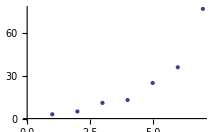

```mathematica
ListPlot[liste3]
```

Tracer une liste en représentant la ligne qui joint les points ;

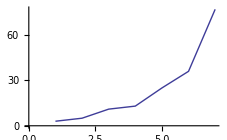

```mathematica
ListPlot[liste3,Joined->True]
```

On peut le faire aussi avec :

```mathematica
ListLinePlot[liste3]==ListPlot[liste3,Joined->True]         (* True *)
```

#### 2. Tracer une liste de deux coordonnées

Pour une liste de deux coordonnées, l’abscisse est la première des coordonnées et l’ordonnée la seconde :

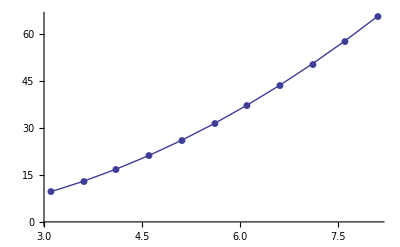

```mathematica
ListPlot[
liste7,
Joined->True,
PlotMarkers->Automatic
]
```

Notez que les points sont rendus visibles avec l’option : PlotMarkers→Automatic

#### 3. Tracer une liste à trois entrées (tracé en courbes de niveaux)

Examinez l’exemple :

```mathematica
liste8=Table[Cos[i]Cos[j],{i,0,2π,0.6},{j,0,2π,0.6}]
```

{{1.,0.825336,0.362358,-0.227202,-0.737394,-0.989992,-0.896758,-0.490261,0.087499,0.634693,0.96017},{0.825336,0.681179,0.299067,-0.187518,-0.608597,-0.817076,-0.740127,-0.40463,0.072216,0.523835,0.792463},{0.362358,0.299067,0.131303,-0.0823284,-0.2672,-0.358731,-0.324947,-0.17765,0.0317059,0.229986,0.347925},{-0.227202,-0.187518,-0.0823284,0.0516208,0.167537,0.224928,0.203745,0.111388,-0.01988,-0.144204,-0.218153},{-0.737394,-0.608597,-0.2672,0.167537,0.543749,0.730014,0.661264,0.361515,-0.0645212,-0.468019,-0.708024},{-0.989992,-0.817076,-0.358731,0.224928,0.730014,0.980085,0.887784,0.485355,-0.0866233,-0.628341,-0.950561},{-0.896758,-0.740127,-0.324947,0.203745,0.661264,0.887784,0.804176,0.439646,-0.0784654,-0.569166,-0.861041},{-0.490261,-0.40463,-0.17765,0.111388,0.361515,0.485355,0.439646,0.240356,-0.0428973,-0.311165,-0.470734},{0.087499,0.072216,0.0317059,-0.01988,-0.0645212,-0.0866233,-0.0784654,-0.0428973,0.00765607,0.055535,0.0840139},{0.634693,0.523835,0.229986,-0.144204,-0.468019,-0.628341,-0.569166,-0.311165,0.055535,0.402835,0.609413},{0.96017,0.792463,0.347925,-0.218153,-0.708024,-0.950561,-0.861041,-0.470734,0.0840139,0.609413,0.921927}}

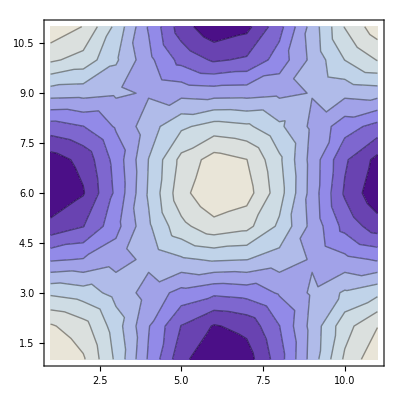

```mathematica
ListContourPlot[liste8]
```

#### 4. Tracer une liste à quatre entrées (animation des tracés)

Examinez l’exemple :

C’est un exemple d’une valeur calculée en fonction de 3 autres : donc un objet en 4 dimensions.
On observe contrairement à ce que l’on dit souvent, que c’est quelque chose que l’on peut très bien représenter. Ici justement avec Mathematica.
C’est d’ailleurs un des objectifs de Mathematica de faire des maths autrement, et notamment ici de représenter des objets comme celui-ci grâce à une animation.
C’est assez joli, et on pourrait faire mieux, avec du volume

```mathematica
liste8=Table[
Cos[i+k(π/30)]Cos[j],
{i,0,2π,0.6},{j,0,2π,0.6},{k,0,30,1}
];
```

```mathematica
ListAnimate[
Map[
ListContourPlot,
liste8
]
]
```

#### 5. Mise en forme de listes avec TableForm[]

TableForm[] est très utile pour mettre sous forme de tableaux :

```mathematica
?TableForm
```

TableForm[list] prints with the elements of list arranged in an array of rectangular cells.

Rappelons liste7 :

```mathematica
liste7
```

{{3.1,9.61},{3.6,12.96},{4.1,16.81},{4.6,21.16},{5.1,26.01},{5.6,31.36},{6.1,37.21},{6.6,43.56},{7.1,50.41},{7.6,57.76},{8.1,65.61}}

```mathematica
liste7MiseEnForme=TableForm[
liste7,
TableHeadings->{None,{"i","i^2"}}
]
```

i | i^2
3.1 | 9.61
3.6 | 12.96
4.1 | 16.81
4.6 | 21.16
5.1 | 26.01
5.6 | 31.36
6.1 | 37.21
6.6 | 43.56
7.1 | 50.41
7.6 | 57.76
8.1 | 65.61

Attention à ne pas confondre liste7 avec liste7MiseEnForme :
on peut faire des calculs avec liste7 mais pas avec liste7MiseEnForme. (rappel : quand Mathematica ne peut pas traiter l’expression, il la ré-écrit à l’identique)

```mathematica
liste7*3
```

{{9.3,28.83},{10.8,38.88},{12.3,50.43},{13.8,63.48},{15.3,78.03},{16.8,94.08},{18.3,111.63},{19.8,130.68},{21.3,151.23},{22.8,173.28},{24.3,196.83}}

```mathematica
liste7MiseEnForme*3
```

3 i | i^2
3.1 | 9.61
3.6 | 12.96
4.1 | 16.81
4.6 | 21.16
5.1 | 26.01
5.6 | 31.36
6.1 | 37.21
6.6 | 43.56
7.1 | 50.41
7.6 | 57.76
8.1 | 65.61

Exemple de mise en forme d’un tableau rectangulaire à 2 dimensions :

```mathematica
TableForm[
Table[Subscript[a, i,j],{i, 1,3,1},{j,1,5,1}]
]
```

a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5)

#### 6. Mise en forme de matrices avec MatrixForm[]

Exemple de mise en forme sous forme matricielle :

```mathematica
MatrixForm[
Table[Subscript[a, i,j],{i, 1,3,1},{j,1,5,1}]
]
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5))

### E. Caractéristiques d’une liste

Ce sont des fonctions très pratiques pour comprendre ce qu’on fait quand on manipule des listes :

#### 1. Length[]

La longueur d’une liste est donnée par la fonction Length[]

Rappelons pour mémoire liste1, liste2, liste7 (liste8 est trop volumineux pour être imprimé) :

```mathematica
liste1
liste2
liste7
```

{a,b,c}

{{a,3},b,{titi,f[x],-√57},grosminet}

{{3.1,9.61},{3.6,12.96},{4.1,16.81},{4.6,21.16},{5.1,26.01},{5.6,31.36},{6.1,37.21},{6.6,43.56},{7.1,50.41},{7.6,57.76},{8.1,65.61}}

```mathematica
Length[liste1]==3
Length[liste2]==4
Length[liste7]==11
Length[liste8]==11
```

Pour gagner un peu de place, il est plus simple de faire :

```mathematica
Map[
Length,
{liste1,liste2, liste7,liste8}
]
```

{3,4,11,11}

#### 2. Dimensions[]

Sa structure simple (rectangulaire à n dimensions) est donnée par Dimensions[]
On observe que la structure interne de liste2 n’est pas vue par Dimensions[] contrairement à celles de liste7 ou liste8.

```mathematica
Map[
Dimensions,
{liste1,liste2, liste7,liste8}
]
```

{{3},{4},{11,2},{11,11}}

#### 3. Short[]

```mathematica
Map[
Short,
{liste1,liste2, liste7,liste8}
]
```

{{a,b,c},{{a,3},b,{titi,f[x],-√57},grosminet},{{3.1,9.61},«9»,{8.1,65.61}},{«1»}}

liste1 et liste2 sont trop petites pour pouvoir faire un résumé.

#### 4. Shallow[]

C’est un résumé plus détaillé (non imprimé pour raison de place).

```mathematica
Map[
Shallow,
{liste1,liste2, liste7,liste8}
]
```

{{a,b,c},{{a,3},b,{titi,f[«1»],Times[«2»]},grosminet},{{3.1,9.61},{3.6,12.96},{4.1,16.81},{4.6,21.16},{5.1,26.01},{5.6,31.36},{6.1,37.21},{6.6,43.56},{7.1,50.41},{7.6,57.76},«1»},{{1.,0.825336,0.362358,-0.227202,-0.737394,-0.989992,-0.896758,-0.490261,0.087499,0.634693,«1»},{0.825336,0.681179,0.299067,-0.187518,-0.608597,-0.817076,-0.740127,-0.40463,0.072216,0.523835,«1»},{0.362358,0.299067,0.131303,-0.0823284,-0.2672,-0.358731,-0.324947,-0.17765,0.0317059,0.229986,«1»},{-0.227202,-0.187518,-0.0823284,0.0516208,0.167537,0.224928,0.203745,0.111388,-0.01988,-0.144204,«1»},{-0.737394,-0.608597,-0.2672,0.167537,0.543749,0.730014,0.661264,0.361515,-0.0645212,-0.468019,«1»},{-0.989992,-0.817076,-0.358731,0.224928,0.730014,0.980085,0.887784,0.485355,-0.0866233,-0.628341,«1»},{-0.896758,-0.740127,-0.324947,0.203745,0.661264,0.887784,0.804176,0.439646,-0.0784654,-0.569166,«1»},{-0.490261,-0.40463,-0.17765,0.111388,0.361515,0.485355,0.439646,0.240356,-0.0428973,-0.311165,«1»},{0.087499,0.072216,0.0317059,-0.01988,-0.0645212,-0.0866233,-0.0784654,-0.0428973,0.00765607,0.055535,«1»},{0.634693,0.523835,0.229986,-0.144204,-0.468019,-0.628341,-0.569166,-0.311165,0.055535,0.402835,«1»},«1»}}

### F. Calcul vectoriel

#### 1. Combinaison linaire

Définissons deux vecteurs dans un espace de dimension 3, définissons les vecteurs u⃗ et v⃗ suivants :

```mathematica
u={u1,u2,u3};
v={v1,v2,v3};
```

On peut faire toutes les opérations de l’espace vectoriel ℝ^3, c’est à dire calculer toutes les combinaisons linéaires de ces vecteurs :

```mathematica
λ u +μ v
```

{u1 λ+v1 μ,u2 λ+v2 μ,u3 λ+v3 μ}

#### 2. Produit scalaire de 2 vecteurs : Dot[]

Cet espace vectoriel est muni du produit scalaire ordinaire (utilisant la base canonique) :

```mathematica
u.v==u1 v1+u2 v2+u3 v3;
```

#### 3. Norme d’un vecteur : Norm[]

Cet espace vectoriel est muni de la norme :

```mathematica
Norm[u]==√(Abs[u1]^2+Abs[u2]^2+Abs[u3]^2);                               (* True *)
```

Attention à ne pas confondre les opérations . et * :

```mathematica
u.v==Dot[u,v]==u1 v1+u2 v2+u3 v3==Apply[Plus,u*v]==Total[u*v]
```

```mathematica
u*v==Times[u,v]=={u1 v1,u2 v2,u3 v3}                                      (* True *)
```

#### 4. Produit vectoriel : Cross[]

On dispose aussi de la définition du produit vectoriel :

```mathematica
Cross[u,v]=={-u3 v2+u2 v3,u3 v1-u1 v3,-u2 v1+u1 v2}     (* True *)
```

### G. Calcul matriciel (cf. aide)

## III. Programmation fonctionnelle et Programmation par règles

En première approximation, ce sont deux modes de programmation très proches dans l’esprit, qui diffèrent principalement par leur mode d’écriture.

#### 1. ReplaceAll[] et Rule[]

La programmation par règles consiste à utiliser des règles de remplacement.
Dans l'exemple suivant, l'élément a de la liste {a, b, c} est remplacé par b selon :

```mathematica
{a,b,c}/.a->b
```

{b,b,c}

Détaillons cette expression :

/.  est la notation de type Infix de la fonction ReplaceAll[].
Elle prend ici comme argument la liste {a, b, c} (et plus généralement une expression), 
et comme second argument la règle de remplacement a → b.

```mathematica
({a,b,c}/.a->b)==ReplaceAll[{a,b,c},a->b]=={b,b,c}
```

True

a → b  est la notation de type Infix de la fonction Rule[a, b]

```mathematica
Rule[a,b]
```

a→b

#### 2. Pattern[]

L'intérêt de la programmation par règles est d'être associée aux Pattern[], c'est-à-dire à des motifs (et au typage).
Dans cet exemple, on remplace toutes les puissances de x^p par f[p] :

```mathematica
1 + x^2 + x^4 /. x^p_ -> f[p]
```

1+f[2]+f[4]

#### 3. Usages des règles de remplacement

Attention aux petites subtilités suivantes :

Dans cette expression, les règles sont appliquées en une seule fois, et l’on obtient :

```mathematica
(x+3y)/.{x->y,y->z}
```

y+3 z

Dans cette expression, on effectue les deux mêmes transformations mais successivement pour obtenir :

```mathematica
(x+3y)/.{x->y}/.{y->z}
```

4 z

Notez que ce mode d’écriture est ici plus clair que de faire un remplacement répété comme ci-dessous :

```mathematica
(x+3y)//.{x->y,y->z}
```

4 z

Application : Un brin d’ADN est constitué de nucléotides : A, T, G, C, écrire la séquence complémentaire.

```mathematica
list9={A,C,G,T,G,T,A,C,G,T,G,T}
```

→ Remplacez dans liste9 tous les A par T, les T par A, les G par C, et les C par G (pour avoir la séquence du brin complémentaire) :

```mathematica
{A,C,G,T,G,T,A,C,G,T,G,T}/. {A -> T,C-> G, G->C, T->A}
```

{T,G,C,A,C,A,T,G,C,A,C,A}

Chaque groupe de trois nucléotides, appelé codon : {A,U,G}, {C, G, C}, etc... donne un acide aminé Met et Gly respectivement.

```mathematica
{A,C,G,T,G,T,A,U, G, C,G,C,G,T} //.{x___,A,U,G,y___}->  {x,Met,y}
```

{A,C,G,T,G,T,Met,C,G,C,G,T}

```mathematica
{A,C,G,T,G,T,A,U, G, C,G,C,G,T} //.{{x___,A,U,G,y___}->  {x,Met,y}, {x___,C,G,C,y___}->  {x,Gly,y}}
```

{A,C,G,T,G,T,Met,Gly,G,T}

## IV. Traitement d’expressions symboliques

### A. Transformations algébriques

#### 1. Expand[]

Développement de l'expression (2x+3)(x^2-6)

```mathematica
Expand[(2x+3)(x^2-6)]==-18-12 x+3 x^2+2 x^3
```

On peut spécifier la partie à développer :

```mathematica
Expand[(a+b)^2(1+x)^2]==a^2+2 a b+b^2+2 a^2 x+4 a b x+2 b^2 x+a^2 x^2+2 a b x^2+b^2 x^2
```

```mathematica
Expand[(a+b)^2(1+x)^2,x]==(a+b)^2+2 (a+b)^2 x+(a+b)^2 x^2
```

```mathematica
Expand[(a+b)^2(1+x)^2,1+x]==(a+b)^2 (1+2 x+x^2)
```

#### 2. Factor[] est l’opération inverse d’Expand[]

Factorisation de l'expression -18-12 x+3 x^2+2 x^3

```mathematica
Factor[-18-12 x+3 x^2+2 x^3]==(2x+3)(x^2-6)
```

Certaines expressions ne sont pas factorisées par Factor (ne fait rien) :

```mathematica
Factor[2+2 √2 x+x^2]
```

Il faut ajouter une option :

```mathematica
Factor[2+2 √2 x+x^2,Extension->Automatic]
```

(√2+x)^2

En cas d’échec, il faut alors spécifier manuellement l’extension (ce mot fait référence à l’extension de Galois) :

```mathematica
Factor[x^4-25]==Factor[x^4-25,Extension -> Automatic]==(-5+x^2) (5+x^2);
Factor[x^4-25,Extension ->√5]
```

-(√5-x) (√5+x) (5+x^2)

### B. Réarrangements algébriques

#### 1. ExpandDenominator, ExpandNumerator

Cf. aide de Mathematica.

ExpandDenominator expands out products and powers that appear as denominators in expr.
ExpandNumerator expands out products and powers that appear in the numerator of expr.

#### 2. Together[], Apart[], Cancel[]

cf. Aide
Together puts terms in a sum over a common denominator, and cancels factors in the result.
Apart rewrites a rational expression as a sum of terms with minimal denominators.
Cancel cancels out common factors in the numerator and denominator of expr.

#### 3. Applications

→ Factoriser x^2-3 avec Mathematica.

```mathematica
Factor[x^2-3]
Factor[x^2-3,Extension -> Automatic]
Factor[x^2-3,Extension -> Sqrt[3]]
```

-3+x^2

-3+x^2

-(√3-x) (√3+x)

→ Soit f[x]=((x+3)(x-1)^2)/((x^2+1)(x+5)^2). Utiliser les fonctions Expand, ExpandAll, ExpandDenominator et ExpandNumerator pour f[x] et commenter les résultats.

```mathematica
f[x_]:=((x+3)(x-1)^2)/((x^2+1)(x+5)^2)
```

Ne développe que le numérateur :

```mathematica
Expand[((x+3)(x-1)^2)/((x^2+1)(x+5)^2)]
```

3/((5+x)^2 (1+x^2))-(5 x)/((5+x)^2 (1+x^2))+x^2/((5+x)^2 (1+x^2))+x^3/((5+x)^2 (1+x^2))

Développe le numérateur et le dénominateur :

```mathematica
ExpandAll[((x+3)(x-1)^2)/((x^2+1)(x+5)^2)]
```

3/(25+10 x+26 x^2+10 x^3+x^4)-(5 x)/(25+10 x+26 x^2+10 x^3+x^4)+x^2/(25+10 x+26 x^2+10 x^3+x^4)+x^3/(25+10 x+26 x^2+10 x^3+x^4)

Ne développe que le numérateur :

```mathematica
ExpandNumerator[((x+3)(x-1)^2)/((x^2+1)(x+5)^2)]
```

(3-5 x+x^2+x^3)/((5+x)^2 (1+x^2))

Ne développe que le dénominateur :

```mathematica
ExpandDenominator[((x+3)(x-1)^2)/((x^2+1)(x+5)^2)]
```

((-1+x)^2 (3+x))/(25+10 x+26 x^2+10 x^3+x^4)

→ Rechercher les fonctions Mathematica qui transforment (en une ou plusieurs étapes) f(x)=1/(x^2-16)-(x+4)/(x^2-3 x-4) en g[x]=(-15-7 x-x^2)/(-16-16 x+x^2+x^3)

Ne développe que le numérateur :

```mathematica
Expand[1/(x^2-16)-(x+4)/(x^2-3 x-4)]
```

1/(-16+x^2)-4/(-4-3 x+x^2)-x/(-4-3 x+x^2)

Ne change rien :

```mathematica
Simplify[1/(x^2-16)-(x+4)/(x^2-3 x-4)]
```

(4+x)/(4+3 x-x^2)+1/(-16+x^2)

Donne l’expression cherchée :

```mathematica
Together[1/(x^2-16)-(x+4)/(x^2-3 x-4)]
```

(-15-7 x-x^2)/((-4+x) (1+x) (4+x))

```mathematica
ExpandDenominator[Together[1/(x^2-16)-(x+4)/(x^2-3 x-4)]]
```

(-15-7 x-x^2)/(-16-16 x+x^2+x^3)

### C. Transformer des expressions trigonométriques

#### 1. Introduction

Les fonctions de transformation d’expression algébrique comme Expand ou Factor laissent inchangées les expressions trigonométriques.

Pour transformer des expressions trigonométriques (et algébriques), on utilise les fonctions qui contiennent le préfixe “Trig”, comme pour TrigExpand ou TrigFactor :

```mathematica
TrigExpand[Sin[x+y]]==Cos[y] Sin[x]+Cos[x] Sin[y]
TrigFactor[Sin[x]^2+Tan[x]^2] ==1/2 (3+Cos[2 x]) Tan[x]^2
```

Les trois fonctions Simplify, FullSimplify et ComplexExpand (voir Suppléments) sont capables de transformer à la fois des expressions algébriques et trigonométriques. Il n’existe donc pas de version “Trig” de ces trois fonctions.
Les formules d’identités trigonométriques peuvent être trouvées sur Wikipedia en français :
	http://fr.wikipedia.org/wiki/Identité_trigonométrique
Mais il y a plus de détails sur la page équivalente en anglais (cliquer sur English à gauche sous Autres langues) :
	http://en.wikipedia.org/wiki/List_of_trigonometric_identities

#### 2. TrigExpand[]

TrigExpand développe une expressions en deux étapes :

1. Séparation des sommes et multiples entiers des arguments d’une fonction trigonométrique :

```mathematica
TrigExpand[Sin[2*x]]==2 Cos[x] Sin[x]
TrigExpand[Cos[2*y]]==Cos[y]^2-Sin[y]^2
TrigExpand[Sin[x+y]]==Cos[y] Sin[x]+Cos[x] Sin[y]
```

2. Ensuite développement de produits de fonctions trigonométriques en sommes de puissances :

```mathematica
TrigExpand[Sin[2*x]]*TrigExpand[Cos[2*y]]
TrigExpand[Sin[2*x]*Cos[2*y]]
```

2 Cos[x] Sin[x] (Cos[y]^2-Sin[y]^2)

2 Cos[x] Cos[y]^2 Sin[x]-2 Cos[x] Sin[x] Sin[y]^2

Dans cet exemple les deux calculs donnent le même résultat, car aucune identité trigonométrique n’est appliquée à la deuxième étape de TrigExpand.

Exemple où une identité trigonométrique est appliquée à la deuxième étape :

```mathematica
TrigExpand[Sin[x]^2*Cos[y]]
```

Cos[y]/2-1/2 Cos[x]^2 Cos[y]+1/2 Cos[y] Sin[x]^2

#### 3. TrigFactor[]

TrigFactor essaie de factoriser une expression en utilisant les identités trigonométriques. Elle peut changer les arguments des fonctions trigonométriques. Exemple :

```mathematica
TrigFactor[Cos[y]*Sin[x]+Cos[x]*Sin[y]] ==Sin[x+y]
TrigFactor[Sin[x]+Cos[x]]==√2 Sin[π/4+x]
```

#### 4. TrigReduce[]

La fonction TrigReduce transforme des expressions trigonométriques en combinant les arguments ou en appliquant les règles d’identité d’angles multiples. Exemples :

```mathematica
TrigReduce[2*Sin[x]*Cos[y]]==Sin[x-y]+Sin[x+y]  (* True *)
TrigReduce[2*Cos[x]^2]==1+Cos[2 x]                                       (* True *)
```

En général TrigReduce est la fonction inverse de TrigExpand :

```mathematica
Sin[2*x]==TrigReduce[TrigExpand[Sin[2*x]]];              (* True *)
Sin[x+y] ==TrigReduce[TrigExpand[Sin[x+y]]];
```

→ TrigFactor peut donner dans certains cas le résultat inverse de TrigExpand. Tester les deux exemples. Dans lesquels des deux cas TrigFactor donne le résultat inverse de TrigExpand et pourquoi ?

```mathematica
TrigExpand[Sin[2*x]]==2 Cos[x] Sin[x]==TrigFactor[TrigExpand[Sin[2*x]]];
```

Ici 2 Cos[x] Sin[x] est déjà factorisé par TrigExpand et TrigFactor ne change rien (et ne redonne pas Sin[2*x]).

```mathematica
TrigExpand[Sin[x+y]]==Cos[y] Sin[x]+Cos[x] Sin[y];
```

```mathematica
TrigFactor[TrigExpand[Sin[x+y]]]==Sin[x+y];
```

Ici Cos[y] Sin[x]+Cos[x] Sin[y] n’est pas encore factorisé.

→ Appliquer TrigReduce sur f(x, y, z) =(sin(x))^2 cos(y) sin(z)  et TrigFactor sur le résultat. Commenter.

```mathematica
f[x_,y_,z_]:=Sin[x]^2*Cos[y]*Sin[z]
```

```mathematica
TrigReduce[f[x,y,z]]
```

1/8 (Sin[2 x-y-z]-2 Sin[y-z]+Sin[2 x+y-z]-Sin[2 x-y+z]+2 Sin[y+z]-Sin[2 x+y+z])

```mathematica
TrigFactor[TrigReduce[f[x,y,z]]]
```

Cos[y] Sin[x]^2 Sin[z]

Ici TrigFactor, et non TrigExpand, est la fonction inverse de TrigReduce.

```mathematica
TrigExpand[TrigReduce[f[x,y,z]]]
```

1/2 Cos[y] Sin[z]-1/2 Cos[x]^2 Cos[y] Sin[z]+1/2 Cos[y] Sin[x]^2 Sin[z]

```mathematica
TrigExpand[TrigReduce[f[x,y,z]]]//Simplify
```

Cos[y] Sin[x]^2 Sin[z]

```mathematica
Simplify[TrigReduce[f[x,y,z]]]
```

Cos[y] Sin[x]^2 Sin[z]

→ Comparer et commenter les trois résultats des fonctions TrigExpand, TrigReduce et TrigFactor appliquées à f(x)=(sin(x))^2+(tan(x))^2

```mathematica
Clear[f]
```

```mathematica
f [x_]:=Sin[x]^2+Tan[x]^2
```

```mathematica
TrigExpand[f[x]]
```

-1/2-Cos[x]^2/8+(5 Sec[x]^2)/8+(3 Sin[x]^2)/4+Tan[x]^2/2-1/8 Sin[x]^2 Tan[x]^2

On observe que la somme des deux termes (sin(x))^2 et (tan(x))^2 peut être comme la somme d’autant de termes, tandis TrigExpand ne propose rien pour chacun des termes séparément :

```mathematica
TrigExpand[Sin[x]^2]==Sin[x]^2;
TrigExpand[Tan[x]^2]==Tan[x]^2;
```

```mathematica
TrigReduce[f[x]]
```

1/8 (5 Sec[x]^2-4 Cos[2 x] Sec[x]^2-Cos[4 x] Sec[x]^2)

```mathematica
TrigFactor[f[x]]
```

1/2 (3+Cos[2 x]) Tan[x]^2

TrigFactor[] change les arguments et factorise, tandis que TrigReduce[] ne change que les arguments, sans chercher à factoriser.

#### 5. Simplify

Pour retrouver l’expression de départ après TrigExpand ou TrigReduce ou TrigFactor successifs, il peut être nécessaire d’utiliser Simplify :

```mathematica
ClearAll[x,f]
f[x_]:=Sin[2*x]*Cos[2*y]
TrigExpand[f[x]]==2 Cos[x] Cos[y]^2 Sin[x]-2 Cos[x] Sin[x] Sin[y]^2;
TrigFactor[TrigExpand[f[x]]]==4 Cos[x] Sin[x] Sin[π/4-y] Sin[π/4+y];
TrigReduce[TrigExpand[f[x]]]==1/2 (Sin[2 x-2 y]+Sin[2 x+2 y]);
Simplify[TrigFactor[TrigExpand[f[x]]]]==Cos[2 y] Sin[2 x]
Simplify[TrigReduce[TrigExpand[f[x]]]]==Cos[2 y] Sin[2 x]
```

On peut facilement vérifier des identités trigonométriques avec Simplify et ==, comme par exemple :

```mathematica
Simplify[Cos[a+b]==Cos[a]*Cos[b]-Sin[a]*Sin[b]]
```

Application : Vérifier les identités trigonométriques suivantes :
	sin(a + b) = sin(a) cos(b) + cos(a) sin(b)
	(1−cot(a))^2 + (1 − (tan(a)))^2 =(sec(a)−csc(a))^2

```mathematica
Simplify[Sin[a+b]==Sin[a]*Cos[b]+Cos[a]*Sin[b]]
```

```mathematica
Simplify[(1-Cot[a])^2+(1-Tan[a])^2==(Sec[a]-Csc[a])^2]
```

### D. Calculs symboliques

Ces calculs ne sont qu’évoqués ici car ils seront étudiés dans la suite des séances (cf. Aide).

#### 1. Résolution d'équations

Résolution de l'équation x^2-3 x +2 = 0 pour l'inconnue x

```mathematica
Solve[x^2-3x+2==0,x]
```

{{x→1},{x→2}}

On obtient deux solutions réelles. Notez que pour définir une équation, on cherche x tel que l’équation soit égale à 0 : il faut donc utiliser le test "= =" et ne pas confondre avec l'affectation "=".

On observe que les solutions sont données sous forme d’une liste de règles. C’est très pratique et très fonctionnel.
	Vérifions que les solutions sont toutes correctes :

```mathematica
x^2-3x+2==0/.{{x->1},{x->2}}
```

{True,True}

Pour avoir les valeurs des solutions, il suffit de faire :

```mathematica
x/.{{x->1},{x->2}}
```

{1,2}

#### 2. Suites et sommes

```mathematica
Sum[i^2,{i,1,15}]==∑_(i=1)^15 i^2==1240                             (* True *)
```

#### 3. Limite de fonctions

Limite de (x-1) ln(x-1) quand x→ 1

```mathematica
Limit[(x-1) Log[x-1],x->1]==0                            (* True *)
```

#### 4. Dérivée de x^n par rapport à x

```mathematica
D[x^n,x]
```

#### 5. Développement limité

Développement limité de cos(x) autour de x=0 à l'ordre 10

```mathematica
Series[Cos[x],{x,0,10}]
```

#### 6. Primitive ou intégrale indéfinie

Primitive ou intégrale indéfinie de cos(x) :

```mathematica
Integrate[Cos[x],x]==Sin[x]                                     (* True *)
```

Intégrale de ∫_0^∞ e^(-x^2)ⅆx :

```mathematica
Integrate[Exp[-x^2],{x,0,Infinity}]==(√π)/2      (* True *)
```

### E. Calculs numériques

Parfois, un calcul formel n'est pas faisable, mais on peut faire un calcul numérique approché. Quelques exemples :

Calcul d'une valeur approchée de l'intégrale ∫_1^3 ln(arctan(x))ⅆx

```mathematica
NIntegrate[Log[ArcTan[x]],{x,1,3}]
```

0.135924

Calcul approché des solutions de l'équation x^5+3 x^4+2 x^3-x^2+x+1=0
DSolve[x^5+3 x^4+2 x^3-x^2+x+1==0,x] ne donne rien, mais on obtient des racines numériques avec:

```mathematica
NSolve[x^5+3x^4+2x^3-x^2+x+1==0,x]
```

{{x→-1.69305-0.668971 ⅈ},{x→-1.69305+0.668971 ⅈ},{x→-0.566333},{x→0.476216-0.55321 ⅈ},{x→0.476216+0.55321 ⅈ}}

## V. Tracer de fonctions

Pour les principaux types de tracés, on distingue

les tracés de fonctions discrètes :
	2D	ListPlot[], ListLinePlot[],...
	3D	ListPlot3D[], ...

et 		les tracés de fonctions continues :
	2D	Plot[], ParametricPlot[],...		(courbes)
	3D	Plot3D[], ParametricPlot3D[],...	(courbes ou surfaces)

ainsi que 	les tracés en courbe de niveaux
	2D	ContourPlot[]
	3D	ContourPlot3D[]

Voici quelques exemples de tracés de fonctions continues :

Fonction | Exemple | Commande
f[x] | Sin[x]/x | Plot
{f[t],g[t]} | {Sin[3t],Cos[3t]} | ParametricPlot
f[x,y]==0 | x^4-(x^2-y^2)==0 | ContourPlot
f[x,y]≥0 | x^4-(x^2-y^2)≥0 | RegionPlot
r=f[θ] | r=3Cos[5θ] | PolarPlot

et bien d’autres encore (cf. guide/FunctionVisualization)

## VI. Quelques méthodes de programmations

### A. Définition et domaine de définition des variables

#### 1. Motivations

Les affectations de variables sont un casse-tête, car elles sont la première cause de bogue dans un programme procédural. En principe, on devrait ne jamais les utiliser dans un cadre fonctionnel. En pratique, on risque toujours de les utiliser avec le danger permanent d’affectations à mauvais escient, ce qui constitue la bogue la plus courante. Comme c’est une source considérable de perte de temps pour vous, et pour les enseignants qui essaient de comprendre ce qui a pu se passer, et pourquoi “ça ne marche pas !”, alors que “ça devrait marcher !”, voici quelques méthodes très simples pour éviter les inconvénients des affectations.

#### 2. With[]

La fonction With[] pourrait être traduite en français par “Soit[]”. Son intérêt est de déclarer le nom d’une variable, et de réaliser une affectation qui reste strictement locale à la fonction.

Cela comporte beaucoup d’avantages. C’est à peu près équivalent à la phrase du type “soit x=3”. Il est souvent beaucoup plus judicieux de donner un nom plus long informatif, ce qui permet d’expliquer ce que fait la fonction, et de la documenter implicitement. Enfin, dès que la fonction With[] qui encapsule tout un calcul a cessé de calculer, toutes ces affectations locales cessent d’exister. Il n’y alors plus aucun risque.

Il n’est pas possible de déclarer une variable calculée à partir de celles que l’on vient de déclarer dans la même accolade d’un même With[].
Les With[] doivent être emboîtés. On peut et on doit le faire à partir des variables déclarées dans le With[] qui l’emboîte.
With[] est donc contraignant, mais force le programmeur à définir les variables de base (dans le premier With[]), puis celles qui sont calculées à partir de celles-ci (dans le second With[]), et ainsi de suite.

#### 3. Module[]

On peut aussi se passer de With[] en utilisant Module[] qui autorise la définition de variables à partir de variables définies dans Module[]. Il est donc plus puissant, mais moins structurant, et aussi généralement jusqu’à deux fois moins rapide que With[].

### B. Programmation graphique

Résumons ici quelques points qui seront présentés au cours des séances.

La programmation graphique dans Mathematica est tout à fait classique, et correspond dans les grandes lignes à celles qu’on retrouve pour piloter un traceur à feutre, un écran, ou pratiquement dans n’importe quel logiciel graphique.

#### 1. Constitution d’objets graphiques

Dans un premier temps, la programmation graphique consiste à constituer des objets graphiques Graphics[] qui contiennent un dessin décrit par une liste (i.e. un ensemble ordonné) :
	* des spécifications graphiques, couleur, épaisseur des traits, etc, appelés “directives graphiques” (White, Black, Thick[], Dashed[],  ...)
	* des éléments géométriques appelés “primitives graphiques” (Point[], Line[], Arrow[], Circle[], ...)
		à l’aide des fonctions correspondantes,
On peut y adjoindre aussi du texte avec Text[], et des conversions en chaîne de caractères avec ToString[]. 
Ces objets graphiques peuvent être aussi des Plot[], etc... .

#### 2. Assemblage des objets graphiques

Puis dans un second temps, l’assemblage de tous ces objets graphiques est effectué avec la fonction Show[] qui assure le cadrage et la mise à l’échelle avec les options :
	Axes→True, PlotRange → {{xmin, xmax}, {ymin, ymax}}, AspectRatio→1, ImageSize → taille

#### 3. Application

Question 19 du test : On considère 2 vecteurs dans un repère orthonormé : u⃗(2,−1) et v⃗(0, −2). Représenter u⃗ et v⃗ sur un schéma.

Question 20 du test : Sur un nouveau schéma, représenter la somme u⃗ + v⃗ et la différence u⃗ - v⃗ (u⃗ et v⃗ étant les vecteurs définis à la question 19)

Une solution simple de tracé mettant en œuvre les principes ci-dessus :

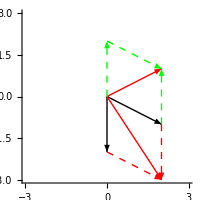

```mathematica
With[
{O={0,0},U={2,-1}, V={0,-2}},
With[
{S=U+V, D=U-V},
Show[
Graphics[
{
(* Solution question 19 en NOIR *)
Thick,Black,Arrow[{O,U}], Arrow[{O,V}],
(* Solution question 20 en ROUGE *)
Red,Arrow[{O,S}], Arrow[{O,D}],
(* Pointillés pour compléter la somme *)
Dashed,Arrow[{U,S}], Arrow[{V,S}],
(* Pointillés pour compléter la différence *)
Green,Arrow[{O,-V}],Arrow[{-V,D}], Arrow[{U,D}]
}
],
(* Cadrage fixe du dessin dans Show *)
Axes->True,PlotRange->{{-3,3},{-3,3}},AspectRatio->1,ImageSize->200
]]]
```

À partir de ces principes, il est possible de concevoir des dessins très sophistiqués.

### C. Interactivité

#### 1. Fonction

Toute expression, et tout particulièrement les tracés graphiques peuvent être rendus interactifs avec Manipulate[] :

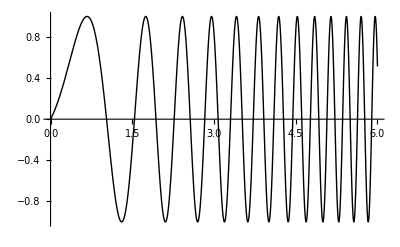

```mathematica
Plot[Sin[x(1+2 x)],{x,0,6},PlotStyle->Black]
```

#### 2. Manipulate

```mathematica
Manipulate[
Plot[Sin[x(1+a x)],{x,0,6},PlotStyle->Black],
{a,0,2}
]
```

## I. Suppléments

### A. Questions liées à l’affectation

#### 1. Règles pour les Noms de Variables et de Fonctions

Les noms de variables et de fonctions définies par l’utilisateur doivent commencer par une minuscule.

La raison est que les noms de toutes les variables et de fonctions prédéfinies dans Mathematica commencent tous par une majuscule. Cette règle simple permet d’une part de savoir d’emblée si une fonction est définie par l’utilisateur ou par Mathematica, et d’autre part, elle permet à Mathematica de rechercher plus rapidement les fonctions définies par l’un ou par l’autre.

Une autre règle implicite est que ces noms sont complets, non abrégés, et non cryptiques.

Enfin, ils respectent les règles usuelles, comme celle de ne pas commencer par un chiffre (ex : 2x), de ne pas contenir des caractères spéciaux (%, #, {, [), ni d’accents, ni d’espace, ni de souligné (tiret bas ou underscore) car ces symboles sont réservés comme nous l’avons vu plus haut.

#### 2. Affectations

L’affectation ne se comporte pas forcément exactement dans un système formel comme Mathematica que dans un contexte de programmation procédurale plus classique.

La raison est que Mathematica est un système. Tout ce que vous envoyez au Noyau par l’intermédiaire de la validation est mémorisé comme une règle à appliquer. Le moteur de Mathematica est un évaluateur (Evaluate) qui applique toutes les règles que vous lui avez données, ainsi que toutes celles dont il dispose pour obtenir un résultat jusqu’à ce qu’il ne varie plus au cours des évaluations successives, et qui vous est ensuite proposé. On imagine assez bien ce type de mécanisme de boucles infinies pour la simplification d’une expression. C’est aussi le cas pour tout calcul.

### B. Tests d’Affectation

#### 1. Mise en place des tests

On cherche ici à tester le comportement d’une suite de commandes. 
On peut écrire ces commandes, soit dans une même cellule en mettant toutes les instructions à la ligne, soit en mettant chaque élément de la liste dans une cellule séparée.
Les listes sont ordonnées. On reproduit donc plus simplement de façon synthétique sur une ligne ce que l’on peut écrire séparément d’une façon ou de l’autre.

Pour être absolument sûr que l’on repart à chaque fois d’un noyau vierge, on fait précéder l’exécution d’un “Quit” (qui doit évidemment être dans une cellule séparée validée séparément : une fois que le noyau est mort, il ne fait plus rien !).

Le premier, ainsi que les états intermédiaires, et le dernier élément donne l’état de {x,y}. On peut donc suivre les différentes étapes réellement effectuées.

#### 2. Affectation immédiate = et affectation retardée :=

```mathematica
(* Quit *) {{x,y},x=Random[],y:=Random[],{x,y},{x,y}}
```

{{0,1},0.430736,Null,{0.430736,0.0381509},{0.430736,0.585249}}

x est défini une fois pour toute par une affectation issue d’un tirage aléatoire.
y n’a pas de valeur initiale, et prend une nouvelle valeur par tirage aléatoire chaque fois que y est invoqué.

#### 3. Affectations numériques de variables, puis calcul

```mathematica
(* Quit *) {{x,y},x=3,y=4,x^2+y^2,{x,y},{x,y}}
```

{{x,y},3,4,25,{3,4},{3,4}}

Tout est très simple.

#### 4. Affectations numériques de variables, et de fonction, puis calcul

```mathematica
(* Quit *) {{x,y},x=5,y=4+x,{x,y},x=10,{x,y},{x,y}}
```

{{x,y},5,9,{5,9},10,{10,9},{10,9}}

y est défini par une affectation qui est une fonction de x, qui a été défini au préalable (x=5).
y est donc affecté de la valeur 9. Cette affectation est définitive, et ne change pas même si x change.

#### 5. Affectations numériques et affectation retardée, puis calcul

```mathematica
(* Quit *)  {{x,y},x=5,y:=4+x,{x,y},x=10,{x,y},x=12,{x,y},{x,y}}
```

{{x,y},5,Null,{5,9},10,{10,14},12,{12,16},{12,16}}

y est défini par une affectation retardée qui est une fonction de x, qui a été défini au préalable (x=5).
y n’est donc pas évalué, et n’a pas de valeur (Null). Par contre y prend ensuite une valeur nouvelle chaque fois que x est modifié et que y est évalué.

Les comportements que l’on observe correspondent bien à ce qu’on attend.

#### 6. Affectations de fonctions, affectations numériques, puis calcul

On obtient (presque) le même comportement dans les deux cas de figures :

```mathematica
(* Quit *) {{x,y},y=4+x,x=5,{x,y},x=10,{x,y},x=12,{x,y}}
```

{{x,y},4+x,5,{5,9},10,{10,14},12,{12,16}}

```mathematica
(* Quit *) {{x,y},y:=4+x,x=5,{x,y},x=10,{x,y},x=12,{x,y}}
```

{{12,16},Null,5,{5,9},10,{10,14},12,{12,16}}

On peut aussi examiner ce que contient la mémoire du noyau :

```mathematica
?x
```

Global`x

x=12

```mathematica
?y
```

Global`y

y=4+x

```mathematica
y
```

16

y est donc bien mémorisé comme une fonction de x, et si x est défini (ici 12), alors y vaut 16.

En résumé, si l’on utilise “=” pour définir des variables et des fonctions, il faut faire très attention à ce qui est vraiment mis en mémoire une valeur ou une fonction d’une variable.

#### 7. Affectations mal conçues et calcul

Exemple de comment faire une boucle infinie avec seulement deux définitions incohérentes :

```mathematica
(* Quit *) {{x,y},y=4+x,x=y+5}
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

{{x,y},4+x,9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+(9+Hold[9+x]))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))}

La raison fondamentale est que l’évaluateur de Mathematica est une boucle infinie qui utilise les expressions données pour atteindre un résultat qui ne varie pas. Or ce résultat qui ne varie pas est impossible à atteindre ici.

### C. Calculs et Nombres complexes

#### 1. Écriture des nombres complexes

Un nombre complexe z=a+ⅈ b est écrit dans Mathematica :

```mathematica
z=a+ⅈ b==a+I b                                             (* True *)
```

Certains calculs peuvent donner des nombres complexes :

```mathematica
Sqrt[-9]==3ⅈ                                                    (* True *)
```

#### 2. Par défaut : a∈ℂ et b∈ℂ

Par défaut, Mathematica suppose que toute variable est complexe. Autrement dit, il suppose que a∈ℂ et b∈ℂ comme on peut l’observer ci-dessous :

```mathematica
z=a+ⅈ b;
Re[z]==-Im[b]+Re[a]                                  (* True *)
Im[z]==Im[a]+Re[b]                                     (* True *)
Abs[z]==Abs[a+ⅈ b]                                      (* True *)
```

#### 2. ComplexExpand, et par défaut : a∈ℝ et b∈ℝ

Il est important de pouvoir supposer que a∈ℝ et b∈ℝ. Pour cela il faut utiliser les fonctions :

```mathematica
z=a+ⅈ b;
ComplexExpand[Re[z]]==a                             (* True *)
ComplexExpand[Im[z]]==b                             (* True *)
ComplexExpand[Abs[z]]==√(a^2+b^2)           (* True *)
```

## Exercices

Cf. le fichier joint M2_4M062UtilisationMMaEtu.nb

## I. Calculs formels

### A. Fonctions essentielles

Dans les calculs ci-dessous, écrivez la suite des opérations que vous devez faire pour  pour aboutir au résultat, en faisant une étape (factorisation OU réduction au même dénominateur OU simplification OU réarrangement , etc ...)

#### 1. ==

→ Calculer au moyen d’une suite d’expressions :

```mathematica
1/(1/3+1/2)==
```

→ Calculer au moyen d’une suite d’expressions :

```mathematica
5/7-2/7(1-3/4)==
```

→ Expliquez dans les grandes lignes comment Mathematica parvient à ce type de résultat.

... Pour la suite des exercices cf. le fichier joint M2_4M062UtilisationMMaEtu.nb à renommer avec votre nom ...

-Graphics-